# Mu3e sensitivity to parameter space

Find our list of signal and background events, along with associated parameters

```mathematica
sigdirs=FileNameJoin[{NotebookDirectory[],"..","muon-decay-newphysics","Events","*"}];
bkgdirs=FileNameJoin[{NotebookDirectory[],"..","muon-decay-background","Events","*"}];
sigfiles=FileNames[FileNameJoin[{sigdirs,"unweighted_events.lhe.gz"}]];
bkgfile=FileNames[FileNameJoin[{bkgdirs,"unweighted_events.lhe.gz"}]];
paramfiles=FileNames[FileNameJoin[{sigdirs,"report.dat"}]];
files=Transpose[{sigfiles,paramfiles}];
nRuns=files//Length;
nb=FileNameJoin[{NotebookDirectory[],"analyze-run.nb"}];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"madevent-analysis.nb"}]]
```

Call our analysis notebook on each set and let us know if it is sensitive or not

```mathematica
paramspace=Reap[
Do[
sig=files[[i,1]];
bkg=bkgfile[[1]];
params=Import[files[[i,2]]];
mphi=params[[3,2]];
gsm=params[[4,2]];
gse=params[[5,2]];
pattern="m_ϕ=``, g_ϕμ=``, g_ϕe=``:";
sensitive=NotebookEvaluate[nb];
Sow[{mphi,gsm,gse,sensitive}];
If[sensitive,Print[StringForm[pattern<>" sensitive",mphi,gsm,gse]];
,Print[StringForm[pattern<>" NOT sensitive",mphi,gsm,gse]]],
{i,nRuns}]][[2]][[1]]
```

Import::chtype: First argument {"/Users/nlange/code/muon-decay-np/sensitivity-analysis/../muon-decay-background/Events/run_001/unweighted_events.lhe.gz"} is not a valid file, directory, or URL specification.

Part::partw: Part 1 of {} does not exist.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed, {} ⟦ 1, 1 ⟧].

Part::partw: Part 1 of {} does not exist.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed, {} ⟦ 1, 1 ⟧].

Part::partw: Part 1 of {} does not exist.

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed, {{} ⟦ 1, 1 ⟧, {} ⟦ 1, 1 ⟧}].

Histogram::ldata: Join[$Failed, $Failed] is not a valid dataset or list of datasets.

HistogramList::ldata: Join[$Failed, $Failed] is not a valid dataset or list of datasets.

Set::shape: Lists {bkgBins, bkgCounts} and HistogramList[Join[$Failed, $Failed], {{0.00012, 0.0002, 0.00028, 0.00036, 0.00044, 0.00052, 0.0006, 0.00068, 0.00076, « 33 », 0.00348, 0.00356, 0.00364, 0.00372, 0.0038, 0.00388, 0.00396, 0.00404, « 364 »}}, bkgScaling\ #2 &] are not the same shape.

Append::normal: Nonatomic expression expected at position 1 in Append[bkgCounts, 0.].

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Transpose::nmtx: The first two levels of the one-dimensional list {bkgBins, 1/2\ 0.\ (0.\ (0.\ (0.\ (0.\ « 2 »))))} cannot be transposed.

ListPlot::lpn: Transpose[{bkgBins, 1/2\ 0.\ (0.\ (0.\ (0.\ « 2 »)))}] is not a list of numbers or pairs of numbers.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Transpose::nmtx: The first two levels of the one-dimensional list {{0.00012, 0.0002, 0.00028, 0.00036, 0.00044, 0.00052, 0.0006, 0.00068, 0.00076, 0.00084, « 31 », 0.0034, 0.00348, 0.00356, 0.00364, 0.00372, 0.0038, 0.00388, 0.00396, 0.00404, « 364 »}, « 1 »} cannot be transposed.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

Transpose::nmtx: The first two levels of the one-dimensional list {bkgBins, 1/2\ 0.\ (0.\ (0.\ (0.\ (0.\ « 2 »))))} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Transpose::nmtx: The first two levels of the one-dimensional list … cannot be transposed.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{{0.0015,1.×10^-6,1.×10^-6,$Failed},{0.0015,1.43845×10^-6,1.×10^-6,{0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(5.40356×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.48427×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(8.28545×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.84451×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.7264×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60886×10^-16)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.26083×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(8.28545×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.15276×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.36616×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.22481×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(8.28545×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.00866×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(8.64569×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.22481×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.00866×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.44095×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.7264×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.00866×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.47697×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(8.28545×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.15276×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.44095×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.15276×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.3689×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.513×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.36616×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.15276×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.04469×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.11674×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.44095×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.33288×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.26083×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.87323×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.72914×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.40492×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.58504×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.54902×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.33288×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.44095×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.47697×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.513×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.83721×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.29685×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.44095×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.26083×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.65709×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.72914×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.76516×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.58504×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.54902×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.44095×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.83721×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.40492×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.65709×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.513×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.87323×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.1254×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.08938×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.3689×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.44961×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.26083×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.69311×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.87323×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.9813×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.76516×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.65709×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.08938×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.40492×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.54902×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.26083×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.87323×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.72914×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.69311×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.34154×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.33288×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.23347×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.83721×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.76516×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.69311×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.15276×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.87323×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.69311×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.58504×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.26083×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.3689×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.72914×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.72914×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.94528×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.76516×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.513×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.65709×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.513×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.54902×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.47697×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.54902×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.11674×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.47697×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.54902×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.76516×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.26083×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.26083×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.76516×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.69311×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.47697×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.54902×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.72914×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.44095×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.7264×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.00866×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.33288×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.54902×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.72914×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.90926×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.18878×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.72914×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.47697×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.08938×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.76516×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.65709×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.513×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.76516×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.33288×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.87323×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.65709×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.83721×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.65709×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.65709×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.65709×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.58504×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.58504×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.22481×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.22481×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.18878×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.44095×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.29685×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.33288×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.33288×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.22481×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.15276×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.54902×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.94528×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.3689×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.47697×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.22481×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.513×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.22481×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.3689×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.9813×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.36616×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.3689×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.47697×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.22481×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.54902×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.15276×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.65709×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.22481×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.40492×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.47697×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(8.28545×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.00593×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.18878×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.513×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.65709×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.69311×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.22481×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.29685×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.62107×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.00866×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.40492×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(8.64569×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.3689×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.04469×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.26083×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.7264×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.00866×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.47697×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.7264×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.3689×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.36616×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.18878×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.20474×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.29685×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.7264×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.7264×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.7264×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.7264×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.56498×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.11674×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.36616×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(8.28545×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.00593×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(8.64569×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.36616×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.84451×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(8.28545×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.00593×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.84451×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.12403×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.00866×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.92522×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.04469×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.12403×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.00866×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.36616×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.20474×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.48427×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(5.76379×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.18878×10^-18)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.12403×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.92522×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(5.76379×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.56498×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.00593×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(5.76379×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.20474×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(5.76379×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.84451×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.48427×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(5.76379×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(4.68308×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.84451×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(4.68308×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(5.76379×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(4.68308×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(9.7264×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(5.76379×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.12403×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(4.68308×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(4.68308×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(5.76379×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(4.68308×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.12403×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(5.76379×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(4.32285×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.96261×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(4.68308×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(5.76379×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.8819×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.8819×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(4.68308×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(6.12403×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.8819×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.24213×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(5.04332×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.8819×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.8819×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.16142×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.24213×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.52166×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.24213×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.96261×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.8819×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.16142×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.24213×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.52166×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.44095×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.16142×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.16142×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.16142×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(2.16142×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.44095×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.08071×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.44095×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.20474×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.20474×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.20474×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.20474×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.20474×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.20474×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.44095×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),(7.20474×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.20474×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.20474×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(1.80119×10^-19)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(7.20474×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),(3.60237×10^-20)/(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0./(3.008×10^-19+{}⟦1,1⟧ (1)),0.}>0.},{0.0015,2.06914×10^-6,1.×10^-6,Null},{0.0015,2.97635×10^-6,1.×10^-6,Null},{0.0015,4.28133×10^-6,1.×10^-6,Null},{0.0015,6.15848×10^-6,1.×10^-6,Null},{0.0015,8.85867×10^-6,1.×10^-6,Null},{0.0015,0.0000127428,1.×10^-6,Null},{0.0015,0.0000183298,1.×10^-6,Null},{0.0015,0.0000263665,1.×10^-6,Null},{0.0015,0.0000379269,1.×10^-6,Null},{0.0015,0.000054556,1.×10^-6,Null},{0.0015,0.000078476,1.×10^-6,Null},{0.0015,0.000112884,1.×10^-6,Null},{0.0015,0.000162378,1.×10^-6,Null},{0.0015,0.000233572,1.×10^-6,Null},{0.0015,0.000335982,1.×10^-6,Null},{0.0015,0.000483293,1.×10^-6,Null},{0.0015,0.000695193,1.×10^-6,Null},{0.0015,0.001,1.×10^-6,Null},{0.00668421,1.×10^-6,1.×10^-6,Null},{0.00668421,1.43845×10^-6,1.×10^-6,Null},{0.00668421,2.06914×10^-6,1.×10^-6,Null},{0.00668421,2.97635×10^-6,1.×10^-6,Null},{0.00668421,4.28133×10^-6,1.×10^-6,Null},{0.00668421,6.15848×10^-6,1.×10^-6,Null},{0.00668421,8.85867×10^-6,1.×10^-6,Null},{0.00668421,0.0000127428,1.×10^-6,Null},{0.00668421,0.0000183298,1.×10^-6,Null},{0.00668421,0.0000263665,1.×10^-6,Null},{0.00668421,0.0000379269,1.×10^-6,Null},{0.00668421,0.000054556,1.×10^-6,Null},{0.00668421,0.000078476,1.×10^-6,Null},{0.00668421,0.000112884,1.×10^-6,Null},{0.00668421,0.000162378,1.×10^-6,Null},{0.00668421,0.000233572,1.×10^-6,Null},{0.00668421,0.000335982,1.×10^-6,Null},{0.00668421,0.000483293,1.×10^-6,Null},{0.00668421,0.000695193,1.×10^-6,Null},{0.00668421,0.001,1.×10^-6,Null},{0.0118684,1.×10^-6,1.×10^-6,Null},{0.0118684,1.43845×10^-6,1.×10^-6,Null},{0.0118684,2.06914×10^-6,1.×10^-6,Null},{0.0118684,2.97635×10^-6,1.×10^-6,Null},{0.0118684,4.28133×10^-6,1.×10^-6,Null},{0.0118684,6.15848×10^-6,1.×10^-6,Null},{0.0118684,8.85867×10^-6,1.×10^-6,Null},{0.0118684,0.0000127428,1.×10^-6,Null},{0.0118684,0.0000183298,1.×10^-6,Null},{0.0118684,0.0000263665,1.×10^-6,Null},{0.0118684,0.0000379269,1.×10^-6,Null},{0.0118684,0.000054556,1.×10^-6,Null},{0.0118684,0.000078476,1.×10^-6,Null},{0.0118684,0.000112884,1.×10^-6,Null},{0.0118684,0.000162378,1.×10^-6,Null},{0.0118684,0.000233572,1.×10^-6,Null},{0.0118684,0.000335982,1.×10^-6,Null},{0.0118684,0.000483293,1.×10^-6,Null},{0.0118684,0.000695193,1.×10^-6,Null},{0.0118684,0.001,1.×10^-6,Null},{0.0170526,1.×10^-6,1.×10^-6,Null},{0.0170526,1.43845×10^-6,1.×10^-6,Null},{0.0170526,2.06914×10^-6,1.×10^-6,Null},{0.0170526,2.97635×10^-6,1.×10^-6,Null},{0.0170526,4.28133×10^-6,1.×10^-6,Null},{0.0170526,6.15848×10^-6,1.×10^-6,Null},{0.0170526,8.85867×10^-6,1.×10^-6,Null},{0.0170526,0.0000127428,1.×10^-6,Null},{0.0170526,0.0000183298,1.×10^-6,Null},{0.0170526,0.0000263665,1.×10^-6,Null},{0.0170526,0.0000379269,1.×10^-6,Null},{0.0170526,0.000054556,1.×10^-6,Null},{0.0170526,0.000078476,1.×10^-6,Null},{0.0170526,0.000112884,1.×10^-6,Null},{0.0170526,0.000162378,1.×10^-6,Null},{0.0170526,0.000233572,1.×10^-6,Null},{0.0170526,0.000335982,1.×10^-6,Null},{0.0170526,0.000483293,1.×10^-6,Null},{0.0170526,0.000695193,1.×10^-6,Null},{0.0170526,0.001,1.×10^-6,Null},{0.0222368,1.×10^-6,1.×10^-6,Null},{0.0222368,1.43845×10^-6,1.×10^-6,Null},{0.0222368,2.06914×10^-6,1.×10^-6,Null},{0.0222368,2.97635×10^-6,1.×10^-6,Null},{0.0222368,4.28133×10^-6,1.×10^-6,Null},{0.0222368,6.15848×10^-6,1.×10^-6,Null},{0.0222368,8.85867×10^-6,1.×10^-6,Null},{0.0222368,0.0000127428,1.×10^-6,Null},{0.0222368,0.0000183298,1.×10^-6,Null},{0.0222368,0.0000263665,1.×10^-6,Null},{0.0222368,0.0000379269,1.×10^-6,Null},{0.0222368,0.000054556,1.×10^-6,Null},{0.0222368,0.000078476,1.×10^-6,Null},{0.0222368,0.000112884,1.×10^-6,Null},{0.0222368,0.000162378,1.×10^-6,Null},{0.0222368,0.000233572,1.×10^-6,Null},{0.0222368,0.000335982,1.×10^-6,Null},{0.0222368,0.000483293,1.×10^-6,Null},{0.0222368,0.000695193,1.×10^-6,Null},{0.0222368,0.001,1.×10^-6,Null},{0.0274211,1.×10^-6,1.×10^-6,Null},{0.0274211,1.43845×10^-6,1.×10^-6,Null},{0.0274211,2.06914×10^-6,1.×10^-6,Null},{0.0274211,2.97635×10^-6,1.×10^-6,Null},{0.0274211,4.28133×10^-6,1.×10^-6,Null},{0.0274211,6.15848×10^-6,1.×10^-6,Null},{0.0274211,8.85867×10^-6,1.×10^-6,Null},{0.0274211,0.0000127428,1.×10^-6,Null},{0.0274211,0.0000183298,1.×10^-6,Null},{0.0274211,0.0000263665,1.×10^-6,Null},{0.0274211,0.0000379269,1.×10^-6,Null},{0.0274211,0.000054556,1.×10^-6,Null},{0.0274211,0.000078476,1.×10^-6,Null},{0.0274211,0.000112884,1.×10^-6,Null},{0.0274211,0.000162378,1.×10^-6,Null},{0.0274211,0.000233572,1.×10^-6,Null},{0.0274211,0.000335982,1.×10^-6,Null},{0.0274211,0.000483293,1.×10^-6,Null},{0.0274211,0.000695193,1.×10^-6,Null},{0.0274211,0.001,1.×10^-6,Null},{0.0326053,1.×10^-6,1.×10^-6,Null},{0.0326053,1.43845×10^-6,1.×10^-6,Null},{0.0326053,2.06914×10^-6,1.×10^-6,Null},{0.0326053,2.97635×10^-6,1.×10^-6,Null},{0.0326053,4.28133×10^-6,1.×10^-6,Null},{0.0326053,6.15848×10^-6,1.×10^-6,Null},{0.0326053,8.85867×10^-6,1.×10^-6,Null},{0.0326053,0.0000127428,1.×10^-6,Null},{0.0326053,0.0000183298,1.×10^-6,Null},{0.0326053,0.0000263665,1.×10^-6,Null},{0.0326053,0.0000379269,1.×10^-6,Null},{0.0326053,0.000054556,1.×10^-6,Null},{0.0326053,0.000078476,1.×10^-6,Null},{0.0326053,0.000112884,1.×10^-6,Null},{0.0326053,0.000162378,1.×10^-6,Null},{0.0326053,0.000233572,1.×10^-6,Null},{0.0326053,0.000335982,1.×10^-6,Null},{0.0326053,0.000483293,1.×10^-6,Null},{0.0326053,0.000695193,1.×10^-6,Null},{0.0326053,0.001,1.×10^-6,Null},{0.0377895,1.×10^-6,1.×10^-6,Null},{0.0377895,1.43845×10^-6,1.×10^-6,Null},{0.0377895,2.06914×10^-6,1.×10^-6,Null},{0.0377895,2.97635×10^-6,1.×10^-6,Null},{0.0377895,4.28133×10^-6,1.×10^-6,Null},{0.0377895,6.15848×10^-6,1.×10^-6,Null},{0.0377895,8.85867×10^-6,1.×10^-6,Null},{0.0377895,0.0000127428,1.×10^-6,Null},{0.0377895,0.0000183298,1.×10^-6,Null},{0.0377895,0.0000263665,1.×10^-6,Null},{0.0377895,0.0000379269,1.×10^-6,Null},{0.0377895,0.000054556,1.×10^-6,Null},{0.0377895,0.000078476,1.×10^-6,Null},{0.0377895,0.000112884,1.×10^-6,Null},{0.0377895,0.000162378,1.×10^-6,Null},{0.0377895,0.000233572,1.×10^-6,Null},{0.0377895,0.000335982,1.×10^-6,Null},{0.0377895,0.000483293,1.×10^-6,Null},{0.0377895,0.000695193,1.×10^-6,Null},{0.0377895,0.001,1.×10^-6,Null},{0.0429737,1.×10^-6,1.×10^-6,Null},{0.0429737,1.43845×10^-6,1.×10^-6,Null},{0.0429737,2.06914×10^-6,1.×10^-6,Null},{0.0429737,2.97635×10^-6,1.×10^-6,Null},{0.0429737,4.28133×10^-6,1.×10^-6,Null},{0.0429737,6.15848×10^-6,1.×10^-6,Null},{0.0429737,8.85867×10^-6,1.×10^-6,Null},{0.0429737,0.0000127428,1.×10^-6,Null},{0.0429737,0.0000183298,1.×10^-6,Null},{0.0429737,0.0000263665,1.×10^-6,Null},{0.0429737,0.0000379269,1.×10^-6,Null},{0.0429737,0.000054556,1.×10^-6,Null},{0.0429737,0.000078476,1.×10^-6,Null},{0.0429737,0.000112884,1.×10^-6,Null},{0.0429737,0.000162378,1.×10^-6,Null},{0.0429737,0.000233572,1.×10^-6,Null},{0.0429737,0.000335982,1.×10^-6,Null},{0.0429737,0.000483293,1.×10^-6,Null},{0.0429737,0.000695193,1.×10^-6,Null},{0.0429737,0.001,1.×10^-6,Null},{0.0481579,1.×10^-6,1.×10^-6,Null},{0.0481579,1.43845×10^-6,1.×10^-6,Null},{0.0481579,2.06914×10^-6,1.×10^-6,Null},{0.0481579,2.97635×10^-6,1.×10^-6,Null},{0.0481579,4.28133×10^-6,1.×10^-6,Null},{0.0481579,6.15848×10^-6,1.×10^-6,Null},{0.0481579,8.85867×10^-6,1.×10^-6,Null},{0.0481579,0.0000127428,1.×10^-6,Null},{0.0481579,0.0000183298,1.×10^-6,Null},{0.0481579,0.0000263665,1.×10^-6,Null},{0.0481579,0.0000379269,1.×10^-6,Null},{0.0481579,0.000054556,1.×10^-6,Null},{0.0481579,0.000078476,1.×10^-6,Null},{0.0481579,0.000112884,1.×10^-6,Null},{0.0481579,0.000162378,1.×10^-6,Null},{0.0481579,0.000233572,1.×10^-6,Null},{0.0481579,0.000335982,1.×10^-6,Null},{0.0481579,0.000483293,1.×10^-6,Null},{0.0481579,0.000695193,1.×10^-6,Null},{0.0481579,0.001,1.×10^-6,Null},{0.0533421,1.×10^-6,1.×10^-6,Null},{0.0533421,1.43845×10^-6,1.×10^-6,Null},{0.0533421,2.06914×10^-6,1.×10^-6,Null},{0.0533421,2.97635×10^-6,1.×10^-6,Null},{0.0533421,4.28133×10^-6,1.×10^-6,Null},{0.0533421,6.15848×10^-6,1.×10^-6,Null},{0.0533421,8.85867×10^-6,1.×10^-6,Null},{0.0533421,0.0000127428,1.×10^-6,Null},{0.0533421,0.0000183298,1.×10^-6,Null},{0.0533421,0.0000263665,1.×10^-6,Null},{0.0533421,0.0000379269,1.×10^-6,Null},{0.0533421,0.000054556,1.×10^-6,Null},{0.0533421,0.000078476,1.×10^-6,Null},{0.0533421,0.000112884,1.×10^-6,Null},{0.0533421,0.000162378,1.×10^-6,Null},{0.0533421,0.000233572,1.×10^-6,Null},{0.0533421,0.000335982,1.×10^-6,Null},{0.0533421,0.000483293,1.×10^-6,Null},{0.0533421,0.000695193,1.×10^-6,Null},{0.0533421,0.001,1.×10^-6,Null},{0.0585263,1.×10^-6,1.×10^-6,Null},{0.0585263,1.43845×10^-6,1.×10^-6,Null},{0.0585263,2.06914×10^-6,1.×10^-6,Null},{0.0585263,2.97635×10^-6,1.×10^-6,Null},{0.0585263,4.28133×10^-6,1.×10^-6,Null},{0.0585263,6.15848×10^-6,1.×10^-6,Null},{0.0585263,8.85867×10^-6,1.×10^-6,Null},{0.0585263,0.0000127428,1.×10^-6,Null},{0.0585263,0.0000183298,1.×10^-6,Null},{0.0585263,0.0000263665,1.×10^-6,Null},{0.0585263,0.0000379269,1.×10^-6,Null},{0.0585263,0.000054556,1.×10^-6,Null},{0.0585263,0.000078476,1.×10^-6,Null},{0.0585263,0.000112884,1.×10^-6,Null},{0.0585263,0.000162378,1.×10^-6,Null},{0.0585263,0.000233572,1.×10^-6,Null},{0.0585263,0.000335982,1.×10^-6,Null},{0.0585263,0.000483293,1.×10^-6,Null},{0.0585263,0.000695193,1.×10^-6,Null},{0.0585263,0.001,1.×10^-6,Null},{0.0637105,1.×10^-6,1.×10^-6,Null},{0.0637105,1.43845×10^-6,1.×10^-6,Null},{0.0637105,2.06914×10^-6,1.×10^-6,Null},{0.0637105,2.97635×10^-6,1.×10^-6,Null},{0.0637105,4.28133×10^-6,1.×10^-6,Null},{0.0637105,6.15848×10^-6,1.×10^-6,Null},{0.0637105,8.85867×10^-6,1.×10^-6,Null},{0.0637105,0.0000127428,1.×10^-6,Null},{0.0637105,0.0000183298,1.×10^-6,Null},{0.0637105,0.0000263665,1.×10^-6,Null},{0.0637105,0.0000379269,1.×10^-6,Null},{0.0637105,0.000054556,1.×10^-6,Null},{0.0637105,0.000078476,1.×10^-6,Null},{0.0637105,0.000112884,1.×10^-6,Null},{0.0637105,0.000162378,1.×10^-6,Null},{0.0637105,0.000233572,1.×10^-6,Null},{0.0637105,0.000335982,1.×10^-6,Null},{0.0637105,0.000483293,1.×10^-6,Null},{0.0637105,0.000695193,1.×10^-6,Null},{0.0637105,0.001,1.×10^-6,Null},{0.0688947,1.×10^-6,1.×10^-6,Null},{0.0688947,1.43845×10^-6,1.×10^-6,Null},{0.0688947,2.06914×10^-6,1.×10^-6,Null},{0.0688947,2.97635×10^-6,1.×10^-6,Null},{0.0688947,4.28133×10^-6,1.×10^-6,Null},{0.0688947,6.15848×10^-6,1.×10^-6,Null},{0.0688947,8.85867×10^-6,1.×10^-6,Null},{0.0688947,0.0000127428,1.×10^-6,Null},{0.0688947,0.0000183298,1.×10^-6,Null},{0.0688947,0.0000263665,1.×10^-6,Null},{0.0688947,0.0000379269,1.×10^-6,Null},{0.0688947,0.000054556,1.×10^-6,Null},{0.0688947,0.000078476,1.×10^-6,Null},{0.0688947,0.000112884,1.×10^-6,Null},{0.0688947,0.000162378,1.×10^-6,Null},{0.0688947,0.000233572,1.×10^-6,Null},{0.0688947,0.000335982,1.×10^-6,Null},{0.0688947,0.000483293,1.×10^-6,Null},{0.0688947,0.000695193,1.×10^-6,Null},{0.0688947,0.001,1.×10^-6,Null},{0.074079,1.×10^-6,1.×10^-6,Null},{0.074079,1.43845×10^-6,1.×10^-6,Null},{0.074079,2.06914×10^-6,1.×10^-6,Null},{0.074079,2.97635×10^-6,1.×10^-6,Null},{0.074079,4.28133×10^-6,1.×10^-6,Null},{0.074079,6.15848×10^-6,1.×10^-6,Null},{0.074079,8.85867×10^-6,1.×10^-6,Null},{0.074079,0.0000127428,1.×10^-6,Null},{0.074079,0.0000183298,1.×10^-6,Null},{0.074079,0.0000263665,1.×10^-6,Null},{0.074079,0.0000379269,1.×10^-6,Null},{0.074079,0.000054556,1.×10^-6,Null},{0.074079,0.000078476,1.×10^-6,Null},{0.074079,0.000112884,1.×10^-6,Null},{0.074079,0.000162378,1.×10^-6,Null},{0.074079,0.000233572,1.×10^-6,Null},{0.074079,0.000335982,1.×10^-6,Null},{0.074079,0.000483293,1.×10^-6,Null},{0.074079,0.000695193,1.×10^-6,Null},{0.074079,0.001,1.×10^-6,Null},{0.0792632,1.×10^-6,1.×10^-6,Null},{0.0792632,1.43845×10^-6,1.×10^-6,Null},{0.0792632,2.06914×10^-6,1.×10^-6,Null},{0.0792632,2.97635×10^-6,1.×10^-6,Null},{0.0792632,4.28133×10^-6,1.×10^-6,Null},{0.0792632,6.15848×10^-6,1.×10^-6,Null},{0.0792632,8.85867×10^-6,1.×10^-6,Null},{0.0792632,0.0000127428,1.×10^-6,Null},{0.0792632,0.0000183298,1.×10^-6,Null},{0.0792632,0.0000263665,1.×10^-6,Null},{0.0792632,0.0000379269,1.×10^-6,Null},{0.0792632,0.000054556,1.×10^-6,Null},{0.0792632,0.000078476,1.×10^-6,Null},{0.0792632,0.000112884,1.×10^-6,Null},{0.0792632,0.000162378,1.×10^-6,Null},{0.0792632,0.000233572,1.×10^-6,Null},{0.0792632,0.000335982,1.×10^-6,Null},{0.0792632,0.000483293,1.×10^-6,Null},{0.0792632,0.000695193,1.×10^-6,Null},{0.0792632,0.001,1.×10^-6,Null},{0.0844474,1.×10^-6,1.×10^-6,Null},{0.0844474,1.43845×10^-6,1.×10^-6,Null},{0.0844474,2.06914×10^-6,1.×10^-6,Null},{0.0844474,2.97635×10^-6,1.×10^-6,Null},{0.0844474,4.28133×10^-6,1.×10^-6,Null},{0.0844474,6.15848×10^-6,1.×10^-6,Null},{0.0844474,8.85867×10^-6,1.×10^-6,Null},{0.0844474,0.0000127428,1.×10^-6,Null},{0.0844474,0.0000183298,1.×10^-6,Null},{0.0844474,0.0000263665,1.×10^-6,Null},{0.0844474,0.0000379269,1.×10^-6,Null},{0.0844474,0.000054556,1.×10^-6,Null},{0.0844474,0.000078476,1.×10^-6,Null},{0.0844474,0.000112884,1.×10^-6,Null},{0.0844474,0.000162378,1.×10^-6,Null},{0.0844474,0.000233572,1.×10^-6,Null},{0.0844474,0.000335982,1.×10^-6,Null},{0.0844474,0.000483293,1.×10^-6,Null},{0.0844474,0.000695193,1.×10^-6,Null},{0.0844474,0.001,1.×10^-6,Null},{0.0896316,1.×10^-6,1.×10^-6,Null},{0.0896316,1.43845×10^-6,1.×10^-6,Null},{0.0896316,2.06914×10^-6,1.×10^-6,Null},{0.0896316,2.97635×10^-6,1.×10^-6,Null},{0.0896316,4.28133×10^-6,1.×10^-6,Null},{0.0896316,6.15848×10^-6,1.×10^-6,Null},{0.0896316,8.85867×10^-6,1.×10^-6,Null},{0.0896316,0.0000127428,1.×10^-6,Null},{0.0896316,0.0000183298,1.×10^-6,Null},{0.0896316,0.0000263665,1.×10^-6,Null},{0.0896316,0.0000379269,1.×10^-6,Null},{0.0896316,0.000054556,1.×10^-6,Null},{0.0896316,0.000078476,1.×10^-6,Null},{0.0896316,0.000112884,1.×10^-6,Null},{0.0896316,0.000162378,1.×10^-6,Null},{0.0896316,0.000233572,1.×10^-6,Null},{0.0896316,0.000335982,1.×10^-6,Null},{0.0896316,0.000483293,1.×10^-6,Null},{0.0896316,0.000695193,1.×10^-6,Null},{0.0896316,0.001,1.×10^-6,Null},{0.0948158,1.×10^-6,1.×10^-6,Null},{0.0948158,1.43845×10^-6,1.×10^-6,Null},{0.0948158,2.06914×10^-6,1.×10^-6,Null},{0.0948158,2.97635×10^-6,1.×10^-6,Null},{0.0948158,4.28133×10^-6,1.×10^-6,Null},{0.0948158,6.15848×10^-6,1.×10^-6,Null},{0.0948158,8.85867×10^-6,1.×10^-6,Null},{0.0948158,0.0000127428,1.×10^-6,Null},{0.0948158,0.0000183298,1.×10^-6,Null},{0.0948158,0.0000263665,1.×10^-6,Null},{0.0948158,0.0000379269,1.×10^-6,Null},{0.0948158,0.000054556,1.×10^-6,Null},{0.0948158,0.000078476,1.×10^-6,Null},{0.0948158,0.000112884,1.×10^-6,Null},{0.0948158,0.000162378,1.×10^-6,Null},{0.0948158,0.000233572,1.×10^-6,Null},{0.0948158,0.000335982,1.×10^-6,Null},{0.0948158,0.000483293,1.×10^-6,Null},{0.0948158,0.000695193,1.×10^-6,Null},{0.0948158,0.001,1.×10^-6,Null},{0.1,1.×10^-6,1.×10^-6,Null},{0.1,1.43845×10^-6,1.×10^-6,Null},{0.1,2.06914×10^-6,1.×10^-6,Null},{0.1,2.97635×10^-6,1.×10^-6,Null},{0.1,4.28133×10^-6,1.×10^-6,Null},{0.1,6.15848×10^-6,1.×10^-6,Null},{0.1,8.85867×10^-6,1.×10^-6,Null},{0.1,0.0000127428,1.×10^-6,Null},{0.1,0.0000183298,1.×10^-6,Null},{0.1,0.0000263665,1.×10^-6,Null},{0.1,0.0000379269,1.×10^-6,Null},{0.1,0.000054556,1.×10^-6,Null},{0.1,0.000078476,1.×10^-6,Null},{0.1,0.000112884,1.×10^-6,Null},{0.1,0.000162378,1.×10^-6,Null},{0.1,0.000233572,1.×10^-6,Null},{0.1,0.000335982,1.×10^-6,Null},{0.1,0.000483293,1.×10^-6,Null},{0.1,0.000695193,1.×10^-6,Null},{0.1,0.001,1.×10^-6,Null}}

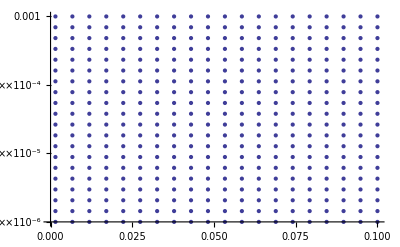

```mathematica
validparams=If[#1[[4]],{#1[[1]],#1[[2]]},##&[]]&/@paramspace;
ListLogPlot[validparams,PlotRange->{{0,0.1},{1*^-6,1*^-3}}]
```

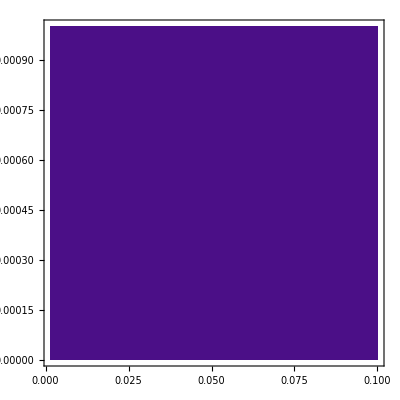

```mathematica
pl=Normal@ListContourPlot[If[#[[4]],{#[[1]],#[[2]],1},{#[[1]],#[[2]],0}]&/@paramspace,Contours->1,InterpolationOrder->0]
(*ListLogLogPlot[Cases[pl,Line[a_,b___]:>a,Infinity],Joined->True,Frame->True,PlotRange->All,AspectRatio->1,PlotStyle->ColorData[1][1]]*)
```